```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
Import["C:\\Users\\KitKa\\QuESTlink\\Link\\QuESTlink.m"]
CreateLocalQuESTEnv["C:\\Users\\KitKa\\QuESTlink\\quest_link.exe"];
(*Import["C:\\Users\\KitKa\\QuESTlink\\RydbergGerardCZ.wl"];*)
(*Import["C:\\Users\\KitKa\\QuESTlink\\RydbergInstaSwapGerardCZ.wl"];*)
(*Import["C:\\Users\\KitKa\\QuESTlink\\RydbergHarvardCZ.wl"];*)
Import["C:\\Users\\KitKa\\QuESTlink\\RydbergGerardCZDCSWAP.wl"];
(*Import["C:\\Users\\KitKa\\QuESTlink\\RydbergHarvardCZDecompSWAP.wl"];*)
(*Import["C:\\Users\\KitKa\\QuESTlink\\RydbergInstaSwapHarvardCZ.wl"];*)
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{1,1,0},{0,0,0},{1,0,0},{2,0,0},{0,1,0},{2,1,0},{0,2,0},{1,2,0},{2,2,0}}}](*,{1,2,0}}}]*),
(* blockade radius in μm*)
BlockadeRadius->Sqrt[2],
(*BlockadeRadius->3,*)
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 98,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[Gates][[All,1]]
RydDev[InitLocations]
data=Import["C:\\Users\\KitKa\\OneDrive\\Documents\\Wolfram Mathematica\\BV5Q.csv"];
data[[5]];
d=data[[5]][[3;;data[[2,1]]+2]];
Length[data]
Fraction[a_,b_]:=a/b
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
```

{Init_q$_Integer,Wait_qubits$__[dur$_]/;Complement[Flatten[{qubits$}],Range[0,userconfig[NQubits]-1]]==={},M_q$_Integer,SRot_q$_Integer[ϕ$_,Δ$_,tg$_],H_q$_Integer,Rx_q$_Integer[θ$_],Ry_q$_Integer[θ$_],Rz_q$_Integer[θ$_],SWAP_(q1$_Integer,q2$_Integer),SWAPLoc_(q1$_Integer,q2$_Integer),ShiftLoc_q$__[v$_]/;LegitShift[Flatten[{q$}],qubitLocs$12338,v$],CZ_(p$_Integer,q$_Integer)[ϕ$_]/;blockadeCheck$12338[{p$,q$}],C_c$_[Z_t$__]/;blockadeCheck$12338[{c$,t$}],C_c$_[Z_t$__[θ$_]]/;blockadeCheck$12338[{c$,t$}],C_c$__[Z_t$_]/;blockadeCheck$12338[{c$,t$}],C_c$__[Z_t$_[θ$_]]}

-Graphics3D-

16

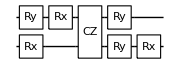
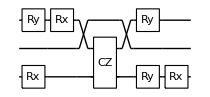
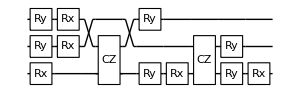
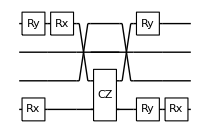
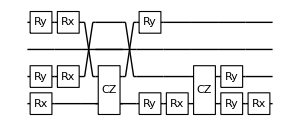
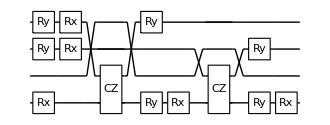
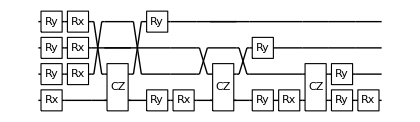
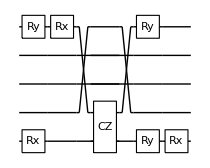
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CircuitTranslator[DataSet_]:=Table[CircSplit=DataSet[[i,3;;DataSet[[i,1]]+2]];
(*Print[CircSplit];*)
Table[GateSplit=StringSplit[CircSplit[[j]],", ["];
GateName=StringTrim[StringTrim[GateSplit[[1]],"["],"'"];
GateQubits=IntegerPart[ToExpression[StringSplit[StringTrim[GateSplit[[2]],"]"],","]]];
GateParameters=If[StringContainsQ[GateName,"C"],Pi,Pi*ToExpression[StringReplace[StringTrim[GateSplit[[3]],"]]"],{"("->"[",")"->"]"}]]];
If[Length[GateQubits]==2,Subscript[ToExpression[GateName], GateQubits[[1]],GateQubits[[2]]][GateParameters],Subscript[ToExpression[GateName], GateQubits[[1]]][GateParameters]],{j,1,DataSet[[i,1]]}]
,{i,1,Length[DataSet]}]
(*a=data[[2;;Length[data]]][[1]][[3;;9]]*)
Table[DrawCircuit[(*ExtractCircuit[InsertCircuitNoise[*)CircuitTranslator[data][[i]](*,RydDev,ReplaceAliases->True]]*)],{i,1,Length[data]}]
```

```mathematica
{Subscript[Init, q$_Integer],Subscript[Wait, qubits$__][dur$_]/;Complement[Flatten[{qubits$}],Range[0,userconfig[NQubits]-1]]==={},Subscript[M, q$_Integer],Subscript[SRot, q$_Integer][ϕ$_,Δ$_,tg$_],Subscript[H, q$_Integer],Subscript[Rx, q$_Integer][θ$_],Subscript[Ry, q$_Integer][θ$_],Subscript[Rz, q$_Integer][θ$_],Subscript[SWAP, q1$_Integer,q2$_Integer],Subscript[SWAPLoc, q1$_Integer,q2$_Integer],Subscript[ShiftLoc, q$__][v$_]/;LegitShift[Flatten[{q$}],qubitLocs$1852814,v$],Subscript[CZ, p$_Integer,q$_Integer][ϕ$_]/;blockadeCheck$1852814[{p$,q$}],Subscript[C, c$_][Subscript[Z, t$__]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$_][Subscript[Z, t$__][θ$_]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$__][Subscript[Z, t$_]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$__][Subscript[Z, t$_][θ$_]]}
```

```mathematica
KetList[NQ_]:=Table[IntegerString[i,2,4],{i,0,2^NQ-1,1}]
KetList[4]
Length[%]
```

{0000,0001,0010,0011,0100,0101,0110,0111,1000,1001,1010,1011,1100,1101,1110,1111}

16

```mathematica
{"0000","0001","0010","0011","0100","0101","0110","0111","1000","1001","1010","1011","1100","1101","1110","1111"}
```

16

```mathematica
percent2infidel[num_]:=Module[{},Assert[0<=num<=100,"number is in percent"];1-0.01 num];
Circs=CircuitTranslator[data];
Meas[q_]:={Subscript[Depol, q][1-0.01*99.7] };
BVCircuitApplier[Circs_,ρ_,Nq_]:= Table[InitZeroState[ρ];ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Join[Table[Subscript[Init, j],{j,0,Nq-1}],Circs[[i]]],RydDev,ReplaceAliases->True]]];Res=CalcProbOfAllOutcomes[ρ,Range[1,Nq-1]]
,{i,1,Length[Circs]}]
(*BVCircuitApplier[Circs_,ρ_,Nq_,NShots_]:= Table[InitZeroState[ρ];ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Join[Table[Subscript[Init, j],{j,0,Nq-1}],Circs[[i]]],RydDev,ReplaceAliases->True]]];
MeasCirc=ExtractCircuit[InsertCircuitNoise[Table[Subscript[M, i],{i,1,Nq-1}],RydDev,ReplaceAliases->True]];
Mean[Table[ρClone=CreateDensityQureg[9];CloneQureg[ρClone,ρ];ApplyCircuit[ρClone,MeasCirc];A=CalcProbOfAllOutcomes[ρClone,Range[1,Nq-1]];DestroyQureg[ρClone];A,{j,1,NShots}]],{i,1,Length[Circs]}]*)
ρ=CreateDensityQureg[9];
Res=BVCircuitApplier[Circs,ρ,5]
i=1
Table[Probs=BVCircuitApplier[Circs[[i;;i+2^Nq]],ρ,Nq];i=i+2^Nq;Probs,{Nq,3,9}]

DestroyAllQuregs[];
```

{{0.965487,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000210763,0.96296,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000210763,0.,0.96296,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{4.65439×10^-8,0.000210211,0.000212655,0.960438,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000210763,0.,0.,0.,0.96296,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{4.65439×10^-8,0.000210211,0.,0.,0.000212655,0.960438,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{4.65439×10^-8,0.,0.000210211,0.,0.000212655,0.,0.960438,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.03966×10^-11,4.64218×10^-8,4.69554×10^-8,0.00020966,4.75013×10^-8,0.000212098,0.000214535,0.95792,0.,0.,0.,0.,0.,0.,0.,0.},{0.000210763,0.,0.,0.,0.,0.,0.,0.,0.96296,0.,0.,0.,0.,0.,0.,0.},{4.65439×10^-8,0.000210211,0.,0.,0.,0.,0.,0.,0.000212655,0.960438,0.,0.,0.,0.,0.,0.},{4.65439×10^-8,0.,0.000210211,0.,0.,0.,0.,0.,0.000212655,0.,0.960438,0.,0.,0.,0.,0.},{1.03966×10^-11,4.64218×10^-8,4.69554×10^-8,0.00020966,0.,0.,0.,0.,4.75013×10^-8,0.000212098,0.000214535,0.95792,0.,0.,0.,0.},{4.65439×10^-8,0.,0.,0.,0.000210211,0.,0.,0.,0.000212655,0.,0.,0.,0.960438,0.,0.,0.},{1.03966×10^-11,4.64218×10^-8,0.,0.,4.69554×10^-8,0.00020966,0.,0.,4.75013×10^-8,0.000212098,0.,0.,0.000214535,0.95792,0.,0.},{1.03966×10^-11,0.,4.64218×10^-8,0.,4.69554×10^-8,0.,0.00020966,0.,4.75013×10^-8,0.,0.000212098,0.,0.000214535,0.,0.95792,0.},{2.34872×10^-15,1.03694×10^-11,1.04872×10^-11,4.63×10^-8,1.06077×10^-11,4.68321×10^-8,4.73642×10^-8,0.00020911,1.07311×10^-11,4.73766×10^-8,4.79149×10^-8,0.000211541,4.84656×10^-8,0.000213972,0.000216403,0.955406}}

```mathematica
x=Range[0,2^4];
y=Range[0,2^4];
Histogram3D[{{0,0}},{{x},{y}},Res&,AxesLabel->{"Resultant State","Input Seed","Probability"},ColorFunction->Function[{height},ColorData["Pastel"][height]]]
```

-Graphics3D-

```mathematica
?CalcProbOfAllOutcomes
```

```mathematica
?QuEST`*
```

```mathematica
?PlotDensityMatrix
```

```mathematica
?DiscretePlot3D
```